FindRoot::nlnum: The function value {0.,-0.717222,-3.66667+e^1.} is not a list of numbers with dimensions {3} at {x,y,z} = {1.,2.,3.}.

```mathematica
f[x_] := 5Cos[x]-4+x^3
```

```mathematica
Plot[f[x],{x,-1,2}]
```

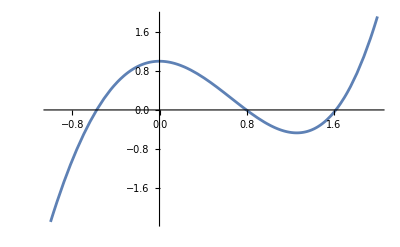

-Graphics-

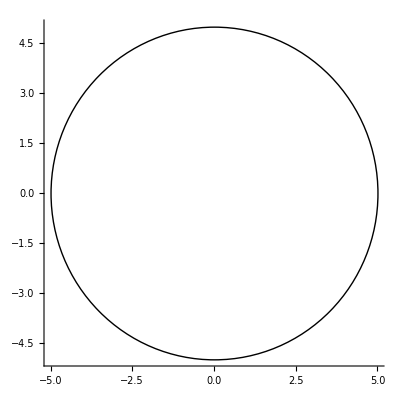

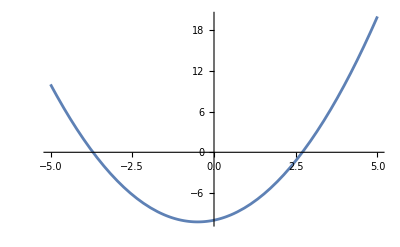

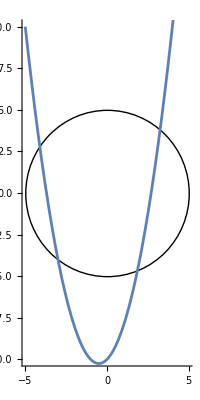

```mathematica
-Graphics-

r1 = Graphics[Circle[{0,0},5],Axes -> True]
r2 = Plot[x^2 + x - 10, {x,-5,5}]
Show[r1,r2,AspectRatio->Automatic,PlotRange->{-10,10}]
```

```mathematica
NSolve[y==x^2+x-10 && x^2 + y^2 == 25]
```

{{x→-3.,y→-4.},{x→3.24846,y→3.80098},{x→1.86907,y→-4.63752},{x→-4.11753,y→2.83654}}

```mathematica
newtow[f_,x0_,tolerance_:10^-6] :=
Module[{xsol,tol,h},{
xsol = x0;
tol = tolerance;
h=2tol;
While[Abs[h]>tol,
h=-f[xsol]/f'[xsol];
xsol = xsol + h];
(xsol,f[xsol]})
}]
```